# Exporter Test

### generate a graph to test on

#### Twine HTML Parser

```mathematica
Clear[generateEdges]
generateEdges[parentName_, links_]:= Thread[DirectedEdge[parentName, links]]
Clear[extractLinks]
extractLinks[passageContent_]:=DeleteCases[StringCases[passageContent,("[["~~ShortestMatch[p___]~~"]]"):> p], {}]
```

```mathematica
Clear[twineParser]
twineParser[absoluteFilePath_String]:=Module[{fileAsString,xmlObject, rootNode,rootNodeName, passages,passageContentThread,passageAssociation,edges,alledges, g, v},
fileAsString = Import[absoluteFilePath, "String"];
xmlObject = parseXML[fileAsString];
rootNode = Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]];
rootNodeName =Cases[xmlObject, XMLElement["tw-storydata", {Rule["name", name_],___}, _]:> name]/.{storytitle_}->storytitle;
passages = Cases[rootNode, XMLElement["tw-passagedata", {___,Rule["name", name_],___}, content_]:> {name,content}, {0, Infinity}];
passageContentThread= AssociationThread[Transpose[passages]⟦1⟧ -> StringReplace[Transpose[passages]⟦2⟧, ("[["~~ShortestMatch[p___]~~"]]"):> p]];
passageAssociation =AssociateTo[passageContentThread, rootNodeName -> "Start Here"];
links= DeleteCases[extractLinks[#⟦2⟧]&/@passages, {}];
edges =generatedEdges[#⟦1⟧, extractLinks[#⟦2⟧]]&/@passages;
alledges= Flatten[{{rootNodeName -> First[passages]⟦1⟧},DeleteCases[edges, {}]}];
g =Graph[alledges];
v =Table[Tooltip[VertexList[g]⟦i⟧, passageAssociation[VertexList[g]⟦i⟧]], {i, 1, Length[VertexList[g]]}];
completeGraph = Graph[v, alledges, VertexLabels->"Name",GraphLayout ->{"LayeredDigraphEmbedding", "RootVertex"->rootNodeName}
]
]
twineParser::usage = "twineParser[path/to/file.html] gives a graph of a Twine 2 project";
```

```mathematica
?twineParser
```

twineParser[path/to/file.html] gives a graph of a Twine 2 project

#### Graphs

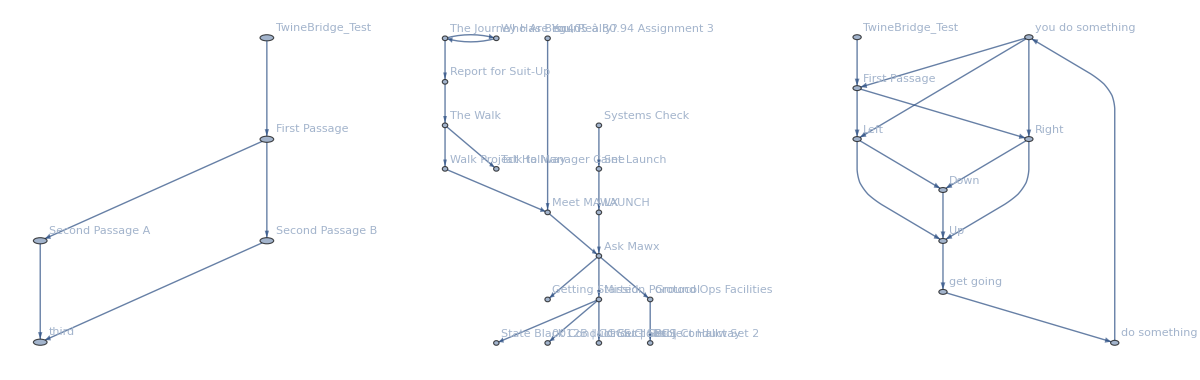

```mathematica
graph1=twineParser["~/Documents/Twine/Stories/TwineBridge_Test.html"];
graph2 = twineParser["~/Documents/Twine/Stories/isc405 _ Assignment 3.html"];
graph3 = twineParser["~/Documents/Twine/Stories/TwineBridge_Test-Medium.html"];
GraphicsRow[{graph1, graph2, graph3}]
```

ONLY PUBLISHED TWINE 2 STORIES WILL WORK — so what does this mean, does that mean if i haven’t  published from twine it won’t work?

Root vertex is the story name. Every vertex, except the root is a passage. Here is a structure I need to follow:

#### Developing Export Procedure

```mathematica
?StringTemplate
```

StringTemplate[string] yields a TemplateObject expression that represents a string template to be applied to arguments. 
StringTemplate[src] uses File[…], URL[…] or CloudObject[…] as the source for the string template.
StringTemplate[form,args] yields a TemplateObject with arguments, suitable for cloud deployment or other evaluation.

— Convert the graph to an association
— Use StringTemplate to fill in data?
—Consider TreePlot

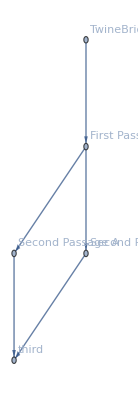

```mathematica
test
```

```mathematica
VertexList[test]
```

{TwineBridge_Test,First Passage,Second Passage A,Second Passage B,third}

```mathematica
EdgeList[test]
```

{TwineBridge_Test->First Passage,First Passage->Second Passage A,First Passage->Second Passage B,Second Passage A->third,Second Passage B->third}

```mathematica
graphExplode[g_Graph]:=Module[{fullFormGraph, graphString, content},
fullFormGraph = FullForm[g];
graphString =ToString[fullFormGraph];
content = StringCases[graphString,("Tooltip, \"")~~Shortest[x__]~~"\"]]":>  x ];
Column@Flatten[{"PASSAGES —————", Framed[#]&/@content}]
]
graphExplode[graph1]
```

PASSAGES —————
Welcome to the third passage.
This is my first passage. Now I'll go to one of two second passages Second Passage A Second Passage B
Go to the third passage
Go to the third passage
Start Here

```mathematica
graphExplode[graph2]
```

PASSAGES —————
May 23rd \[AHat]\200\224 1958. A different Earth, a different time. You are an intergalactic transport pilot. Today you embark on your first state black mission : covert transport operations. Report for Suit-Up Who Are You, Really?
Seryph 6 Launch is go. The ship makes it to Orbit. Mawx performs a post launch check. --- MAWX ::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::::: Confirming Mission Trajectory to -- --- Star Cluster. Ready-up for FTL Travel. Ask Mawx\n\t\t
Project Hallway
Double-click this passage to edit it.
STATE\[AHat]\200\224BLACK CS State Black Conduct Set | SBCS P1 \[AHat]\200\224 Adhere to Conduct Set 0012B | Conduct Set 1 P2 \[AHat]\200\224 Adhere to IGCS Global IGCS Global | Conduct Set 2 
# 10 ... # 9 &amp;nbsp;&amp;nbsp;... # 8 &amp;nbsp;&amp;nbsp;... # 7 &amp;nbsp;&amp;nbsp;... # 6 &amp;nbsp;&amp;nbsp;... # 5 &amp;nbsp;&amp;nbsp;... # 4 &amp;nbsp;&amp;nbsp;... # 3 &amp;nbsp;&amp;nbsp;... # 2 &amp;nbsp;&amp;nbsp;... # 1 &amp;nbsp;&amp;nbsp;...\n\t\t# LAUNCH
Start Here
Piloting Transport Planes since you graduated from College, you joind DeepTransit in 1938. They had just started their Far Reach Initiative to get their Heavy class ships further into space. You worked to transport resources to and from constructs and\n\t\t\tMajor Event Locations. Back To The Story ===&gt; The Journey Has Begun...
The walls are white \[AHat]\200\224 the tunnel is well-lit, there are no corridors, all rooms branch from this hallway. ||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||| Manager Caine: &quot;C46, You heard of it?&quot; You Respond: &quot;Yeah,\n\t\t\tuhh... construction transport, near Aegis-Nine?&quot; Manager Caine: &quot;Yeah, it went offline a few weeks ago and we don&#39;t know why... No spikes prior to target switch, nor emergency telegrams. Surrounding field has no effects, no phsyical abnormalities\n\t\t\tobserved. We need a team to search the construct: there were two other constructs, C35 and C74 \[AHat]\200\224 their systems entered docking procedures without manual control. &quot; You: &quot;Isn&#39;t that what they&#39;re supposed to do? Manager Caine: &quot;When\n\t\t\tthey&#39;re docking, yeah, but they&#39;re hundreds of miles apart&quot; You: &quot;Couldn&#39;t it be a software problem, did you switch it on and off?&quot; Manager Caine: &quot;Ha, yeah I wish, We&#39;ve had our engineers on it since 46 went offline,\n\t\t\tnothing extraordinary in the programs, the behavior persists.&quot; There&#39;s a strange noise coming from further down Project Hallway. You shift your attention back to the mission. You: &quot;Where&#39;s the team?&quot; Manager Caine: &quot;Right,\n\t\t\twe&#39;ll introduce you after equipment breifing&quot; You: &quot;\[AHat]\200\224That&#39;s usually a full crew procedure&quot; Manager Caine: &quot;Not with this crew..&quot; Meet MAWX
Good morning ... I am Mawx (Master\[CapitalAHat]\[NonBreakingSpace]\[AHat]\200\224 Artifiical World Crosser), your galactic transit AI. You may know my siblings... Pawx \[AHat]\200\224 Private Artifical World Crosser Fawx \[AHat]\200\224 First Artificial World Crosser Slawx \[AHat]\200\224 Sub Lane Artifical World Crosser If you do not\n\t\thave a paper manual, you can ask me questions directly... Ask Mawx Let&#39;s get to know eachother :::::::::::::::::::::::::::::::::::::::::::::::\n\n\n\n\n\t
Getting Started Mission Porotocol Ground Ops Facilities
You both leave the suit-up room and head towards the project hallway. ||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||| The excitement is building in you; Project Hallway is a mile long underground tunnel, all pre-flight ground\n\t\t\tops happen here. More importantly, the crew is finally informed of their mission. ||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||||| Walk Project Hallway Talk to Manager Caine
# SYSTEMS CHECK Confiming Route: Earth ..=&gt; // ..=&gt; Aegis-Nine Star Cluster Confirming Mission: Rescue and Retreival Hardware |&gt; :... check Life Support :... check Setup Scripts:... check Set Launch
Welcome to your MAWX series A system. Here you will find information on startup, maintenance and initial usage.
He Says nothing for now...
## A-Deck. 9:30am Manager Caine is at the front of the room \[AHat]\200\224 he has your suit in hand. A neat package, with all the air sucked out. It&#39;s shiny , with a DeepTransit Logo on top. You walk up to him. He looks at you and nods. You have the okay to open\n\t\tyour suit package. *This is it, there&#39;s no turning back.* You take out your DeepTransit pocket knife and carefully slit the package straight down the middle. You feel good. You&#39;re on your way to fulfilling your life-long dream. You let out a\n\t\tsmile, but try to conceal it. Manager Caine catches the slip, &quot;You&#39;re going to do great&quot;, He says. The Walk

```mathematica
graphExplode[graph3]
```

PASSAGES —————
Now that we are going, how about we do something
From here, there are still other places to go. We can go Up or Down
This is my first passage. Where can I go from here? How about Left , or Right?
 Go, Get out of here! 
From here, there are still other places to go. We can go Up or Down
 Hi, I'm doing something, why don't you do something?
Start Here
Now that we are up why don't we get going?
Now that we are down, why don't we get Up?

### Potential Procedure

From | Graph → Association → HTML

	Let’s look at the overall graph structure to see what patterns we need to pay attention to.
	
	What we need are the passage names and their content.
	
	We are also going to need to wrap anything in content that is a PassageName, that way the links to those passages will be created.

```mathematica
testGraph =FullForm[graph1];
```

```mathematica
?Cases
```

Cases[{e_1,e_2,…},pattern] gives a list of the e_i that match the pattern. 
Cases[{e_1,…},pattern→rhs] gives a list of the values of rhs corresponding to the e_i that match the pattern. 
Cases[expr,pattern,levelspec] gives a list of all parts of expr on levels specified by levelspec that match the pattern. 
Cases[expr,pattern→rhs,levelspec] gives the values of rhs that match the pattern. 
Cases[expr,pattern,levelspec,n] gives the first n parts in expr that match the pattern. 
Cases[pattern] represents an operator form of Cases that can be applied to an expression.

```mathematica
ToString[testGraph]
```

Graph[List["TwineBridge_Test", "First Passage", "Second Passage A", "Second Passage B", "third"], List[DirectedEdge["TwineBridge_Test", "First Passage"], DirectedEdge["First Passage", "Second Passage A"], DirectedEdge["First Passage", "Second Passage B"], DirectedEdge["Second Passage A", "third"], DirectedEdge["Second Passage B", "third"]], List[Rule[GraphLayout, List["LayeredDigraphEmbedding", Rule["RootVertex", "TwineBridge_Test"]]], Rule[Properties, List[Rule["third", List[Rule[Tooltip, "Welcome to the third passage."]]], Rule["First Passage", List[Rule[Tooltip, "This is my first passage. Now I'll go to one of two second passages Second Passage A Second Passage B"]]], Rule["Second Passage A", List[Rule[Tooltip, "Go to the third passage"]]], Rule["Second Passage B", List[Rule[Tooltip, "Go to the third passage"]]], Rule["TwineBridge_Test", List[Rule[Tooltip, "Start Here"]]]]], Rule[VertexLabels, List["Name"]]]]

— Rule[“RootVertex”, <story-name>]
<tw-storydata name=”<story-name>” startnode=”1” creator=”WL-TwineBridge” creator-version=”0.01” zoom=”1” format=”Harlowe” format-version=”2.1.0” options=”” hidden>

—

```mathematica
StringTemplate["
<tw-storydata name=\"`StoryTitle`\" startnode=\"1\" creator=\"WL-T\" creator-version=\"2.2.1\" zoom=\"1\" format=\"Harlowe\" format-version=\"2.1.0\" options=\"\" hidden>
  <style role=\"stylesheet\" id=\"twine-user-stylesheet\" type=\"text/twine-css\">



  </style>
  <script role=\"script\" id=\"twine-user-script\" type=\"text/twine-javascript\">



  </script>
  <tw-passagedata pid=\"1\" name=\"First Passage\" tags=\"\" position=\"320,377\" size=\"100,100\">This is my first passage. Now I'll go to one of two second passages [[Second Passage A]] [[Second Passage B]]</tw-passagedata>
  <tw-passagedata pid=\"2\" name=\"Second Passage A\" tags=\"\" position=\"210,527\" size=\"100,100\">Go to the [[third]] passage</tw-passagedata>
  <tw-passagedata pid=\"3\" name=\"Second Passage B\" tags=\"\" position=\"450,527\" size=\"100,100\">Go to the [[third]] passage</tw-passagedata>
  <tw-passagedata pid=\"4\" name=\"third\" tags=\"\" position=\"318,686\" size=\"100,100\">Welcome to the third passage.</tw-passagedata>
</tw-storydata>
"]
```

```mathematica
graph1
```

-Graphics-

```mathematica
Cases[List[Rule[Tooltip, x__String],___]:>  x, All]
```

{}